```mathematica
α=2.;u0=1.*10^-8;
V[r_]=-1/r;
k:=√(2e);δe1={};δe2={};δe3={};δe4={};
```

```mathematica
r2=u0;
```

```mathematica
<<C:\\Users\\ASUS\\Documents\\δe1.mx;
<<C:\\Users\\ASUS\\Documents\\δe2.mx;
<<C:\\Users\\ASUS\\Documents\\δe3.mx;
<<C:\\Users\\ASUS\\Documents\\δe4.mx;
```

```mathematica
δe1
δe2
δe3
δe4
```

{{2.,-0.886406},{2.04139,1.18083},{2.07918,1.52117},{2.11394,0.862939},{2.14613,-0.385603},{2.17609,1.26258},{2.20412,-1.02535},{2.23045,1.24025},{2.25527,0.716186},{2.27875,-0.992574},{2.30103,-1.24718},{2.32222,-1.23152},{2.34242,0.636693},{2.36173,0.950313},{2.38021,1.28047},{2.39794,-0.0214545},{2.41497,1.14122},{2.43136,-1.3743},{2.44716,-0.343035},{2.4624,-1.08435},{2.47712,-0.0205601},{2.49136,0.960226},{2.50515,-0.557488},{2.51851,-1.27283},{2.53148,0.00968828},{2.54407,1.26178},{2.5563,-0.0526718},{2.5682,-0.583388},{2.57978,0.960047},{2.59106,-0.731482},{2.60206,1.04786},{2.61278,0.715457},{2.62325,-0.518484},{2.63347,1.10704},{2.64345,-0.294914},{2.65321,-0.940042},{2.66276,-1.49239},{2.6721,0.3671},{2.68124,-0.981571},{2.6902,1.0355},{2.69897,0.747412},{2.716,-1.15966},{2.73239,-0.171721},{2.74819,-1.02909},{2.76343,-0.0404139},{2.77815,-1.19365},{2.79239,0.603059},{2.80618,-1.29528},{2.81954,1.23837},{2.83251,-0.35645},{2.8451,1.20847},{2.85733,0.731357},{2.86923,-0.825098},{2.88081,0.993722},{2.89209,0.558678},{2.90309,-0.88446},{2.91381,1.06251},{2.92428,0.700991},{2.9345,-0.601422},{2.94448,1.37321},{2.95424,1.09228},{2.96379,-0.0272278},{2.97313,-1.20218},{2.98227,-1.50858},{2.99123,0.790654},{3.,-0.366457},{3.04139,-0.295635},{3.07918,-0.640029},{3.11394,-0.433754},{3.14613,0.559746},{3.17609,1.17901},{3.20412,-1.15447},{3.23045,0.0908037},{3.25527,-1.46619},{3.27875,0.108312},{3.30103,-1.46829},{3.32222,0.168693},{3.34242,-1.23489},{3.36173,0.605868},{3.38021,-0.600405},{3.39794,1.41908},{3.41497,0.37184},{3.43136,-0.607727},{3.44716,-1.52523},{3.4624,0.755648},{3.47712,-0.0548833},{3.47712,-0.0548833},{3.50515,-1.56883},{3.53148,0.0884099},{3.5563,-1.37526},{3.57978,0.596275},{3.60206,-0.384423},{3.62325,-1.52924},{3.64345,0.631666},{3.66276,-0.138488},{3.68124,-1.12436},{3.69897,1.35374},{3.69897,1.35374},{3.74036,-0.386404},{3.77815,1.1508},{3.81291,-0.176461},{3.8451,-1.29282},{3.87506,0.751807},{3.90309,-0.159347},{3.92942,-0.968495},{3.95424,1.35637},{3.97772,0.667745},{4.,0.0714701},{4.17609,-1.04949},{4.30103,-0.238003},{4.39794,1.44825},{4.47712,0.451828},{4.47712,0.451828},{4.54407,-0.283555},{4.60206,-0.837368},{4.65321,-1.27773},{4.69897,1.50483},{4.69897,1.50483},{4.77815,0.96439},{4.8451,0.575553},{4.90309,0.278899},{4.95424,0.0458765},{5.,-0.14022}}

{{2.,-0.566616},{2.04139,-1.32202},{2.07918,0.395192},{2.11394,-0.000404422},{2.14613,-1.2158},{2.17609,1.44768},{2.20412,0.752065},{2.23045,-0.122653},{2.25527,-0.303164},{2.27875,-1.06393},{2.30103,1.51749},{2.32222,1.3522},{2.34242,0.68687},{2.36173,0.270475},{2.38021,0.138758},{2.39794,-0.414431},{2.41497,-0.803798},{2.43136,-0.877822},{2.44716,-1.30584},{2.4624,1.42585},{2.47712,1.36187},{2.49136,1.09609},{2.50515,0.683689},{2.51851,0.528658},{2.53148,0.438139},{2.54407,0.0961805},{2.5563,-0.184211},{2.5682,-0.222957},{2.57978,-0.398409},{2.59106,-0.713367},{2.60206,-0.879633},{2.61278,-0.906718},{2.62325,-1.11186},{2.63347,-1.37821},{2.64345,-1.48073},{2.65321,-1.51573},{2.66276,1.427},{2.6721,1.20017},{2.68124,1.12388},{2.6902,1.09019},{2.69897,0.913589},{2.716,0.639892},{2.73239,0.470846},{2.74819,0.203113},{2.76343,0.0831974},{2.77815,-0.188463},{2.79239,-0.264153},{2.80618,-0.533383},{2.81954,-0.58646},{2.83251,-0.830171},{2.8451,-0.896662},{2.85733,-1.0828},{2.86923,-1.19692},{2.88081,-1.30441},{2.89209,-1.47207},{2.90309,-1.51635},{2.91381,1.4399},{2.92428,1.40243},{2.9345,1.258},{2.94448,1.16968},{2.95424,1.10115},{2.96379,0.959338},{2.97313,0.935522},{2.98227,0.798477},{2.99123,0.745361},{3.,0.672645},{3.04139,0.319201},{3.07918,0.0216905},{3.11394,-0.236153},{3.14613,-0.468831},{3.17609,-0.684331},{3.20412,-0.876763},{3.23045,-1.0342},{3.25527,-1.16247},{3.27875,-1.28766},{3.30103,-1.42001},{3.32222,-1.53291},{3.34242,1.52309},{3.36173,1.4323},{3.38021,1.33583},{3.39794,1.26477},{3.41497,1.1985},{3.43136,1.12011},{3.44716,1.06158},{3.4624,1.00803},{3.47712,0.943276},{3.47712,0.943276},{3.50515,0.849746},{3.53148,0.761085},{3.5563,0.675792},{3.57978,0.601776},{3.60206,0.539142},{3.62325,0.482496},{3.64345,0.428347},{3.66276,0.376743},{3.68124,0.328995},{3.69897,0.285801},{3.69897,0.285801},{3.74036,0.19508},{3.77815,0.118213},{3.81291,0.0493845},{3.8451,-0.00677392},{3.87506,-0.0562684},{3.90309,-0.101201},{3.92942,-0.138619},{3.95424,-0.174548},{3.97772,-0.204361},{4.,-0.233412},{4.17609,-0.412122},{4.30103,-0.502563},{4.39794,-0.557184},{4.47712,-0.593697},{4.47712,-0.593697},{4.54407,-0.619898},{4.60206,-0.639632},{4.65321,-0.654983},{4.69897,-0.667267},{4.69897,-0.667267},{4.77815,-0.685745},{4.8451,-0.698954},{4.90309,-0.708882},{4.95424,-0.716593},{5.,-0.722767},{5.47712,-0.759914}}

{{2.,0.217106},{2.04139,0.0610121},{2.07918,0.00938884},{2.11394,-0.0974521},{2.14613,-0.169038},{2.17609,-0.215193},{2.20412,-0.298203},{2.23045,-0.321463},{2.25527,-0.390182},{2.27875,-0.414979},{2.30103,-0.46131},{2.32222,-0.493285},{2.34242,-0.521241},{2.36173,-0.557497},{2.38021,-0.573947},{2.39794,-0.610353},{2.41497,-0.620824},{2.43136,-0.654608},{2.44716,-0.662493},{2.4624,-0.692438},{2.47712,-0.699464},{2.49136,-0.725391},{2.50515,-0.732265},{2.51851,-0.754529},{2.53148,-0.761428},{2.54407,-0.780585},{2.5563,-0.787451},{2.5682,-0.804082},{2.57978,-0.810779},{2.59106,-0.825404},{2.60206,-0.831793},{2.61278,-0.844849},{2.62325,-0.850818},{2.63347,-0.862657},{2.64345,-0.868123},{2.65321,-0.879023},{2.66276,-0.883937},{2.6721,-0.894109},{2.68124,-0.89845},{2.6902,-0.908053},{2.69897,-0.911824},{2.716,-0.924197},{2.73239,-0.935688},{2.74819,-0.946399},{2.76343,-0.95642},{2.77815,-0.965828},{2.79239,-0.97469},{2.80618,-0.983062},{2.81954,-0.990993},{2.83251,-0.998523},{2.8451,-1.00568},{2.85733,-1.01249},{2.86923,-1.01897},{2.88081,-1.02513},{2.89209,-1.03098},{2.90309,-1.03652},{2.91381,-1.04176},{2.92428,-1.0467},{2.9345,-1.05135},{2.94448,-1.05573},{2.95424,-1.05985},{2.96379,-1.06373},{2.97313,-1.06742},{2.98227,-1.07093},{2.99123,-1.07431},{3.,-1.07757},{3.04139,-1.09295},{3.07918,-1.10648},{3.11394,-1.11696},{3.14613,-1.12612},{3.17609,-1.13475},{3.20412,-1.14156},{3.23045,-1.14785},{3.25527,-1.15375},{3.27875,-1.15846},{3.30103,-1.16318},{3.32222,-1.16729},{3.34242,-1.17088},{3.36173,-1.17452},{3.38021,-1.17746},{3.39794,-1.18045},{3.41497,-1.18312},{3.43136,-1.18551},{3.44716,-1.18794},{3.4624,-1.18993},{3.47712,-1.19205},{3.47712,-1.19205},{3.50515,-1.19562},{3.53148,-1.19878},{3.5563,-1.20163},{3.57978,-1.2042},{3.60206,-1.20653},{3.62325,-1.20863},{3.64345,-1.21052},{3.66276,-1.21224},{3.68124,-1.21381},{3.69897,-1.21526},{3.69897,-1.21526},{3.74036,-1.21847},{3.77815,-1.2211},{3.81291,-1.22334},{3.8451,-1.22529},{3.87506,-1.22695},{3.90309,-1.22841},{3.92942,-1.22971},{3.95424,-1.23085},{3.97772,-1.23188},{4.,-1.23281},{4.17609,-1.23868},{4.30103,-1.24161},{4.39794,-1.24338},{4.47712,-1.24455},{4.47712,-1.24455},{4.54407,-1.2454},{4.60206,-1.24602},{4.65321,-1.24652},{4.69897,-1.24691},{4.69897,-1.24691},{4.77815,-1.2475},{4.8451,-1.24792},{4.90309,-1.24823},{4.95424,-1.24848},{5.,-1.24867},{5.69897,-1.25009},{6.,-1.25027}}

{{2.,-0.256327},{2.04139,-0.261784},{2.07918,-0.265276},{2.11394,-0.269277},{2.14613,-0.271696},{2.17609,-0.274799},{2.20412,-0.276551},{2.23045,-0.279015},{2.25527,-0.280372},{2.27875,-0.282321},{2.30103,-0.28347},{2.32222,-0.284977},{2.34242,-0.286033},{2.36173,-0.287162},{2.38021,-0.288177},{2.39794,-0.289007},{2.41497,-0.289979},{2.43136,-0.290604},{2.44716,-0.291498},{2.4624,-0.292014},{2.47712,-0.292784},{2.49136,-0.293271},{2.50515,-0.293889},{2.51851,-0.294391},{2.53148,-0.29486},{2.54407,-0.295379},{2.5563,-0.295736},{2.5682,-0.296243},{2.57978,-0.296543},{2.59106,-0.296996},{2.60206,-0.29729},{2.61278,-0.29766},{2.62325,-0.297976},{2.63347,-0.29826},{2.64345,-0.298596},{2.65321,-0.298817},{2.66276,-0.299147},{2.6721,-0.299344},{2.68124,-0.299636},{2.6902,-0.299843},{2.69897,-0.300076},{2.716,-0.300485},{2.73239,-0.300875},{2.74819,-0.301251},{2.76343,-0.301608},{2.77815,-0.301939},{2.79239,-0.30224},{2.80618,-0.302511},{2.81954,-0.302761},{2.83251,-0.302999},{2.8451,-0.303232},{2.85733,-0.30346},{2.86923,-0.303679},{2.88081,-0.303883},{2.89209,-0.304068},{2.90309,-0.304239},{2.91381,-0.3044},{2.92428,-0.304558},{2.9345,-0.304715},{2.94448,-0.304869},{2.95424,-0.305015},{2.96379,-0.305151},{2.97313,-0.305275},{2.98227,-0.305392},{2.99123,-0.305506},{3.,-0.305621},{3.04139,-0.306131},{3.07918,-0.306559},{3.11394,-0.30691},{3.14613,-0.307214},{3.17609,-0.307484},{3.20412,-0.307716},{3.23045,-0.307917},{3.25527,-0.308101},{3.27875,-0.308266},{3.30103,-0.308411},{3.32222,-0.308542},{3.34242,-0.308665},{3.36173,-0.308776},{3.38021,-0.308875},{3.39794,-0.308968},{3.41497,-0.309055},{3.43136,-0.309135},{3.44716,-0.309207},{3.4624,-0.309276},{3.47712,-0.309342},{3.47712,-0.309342},{3.50515,-0.309457},{3.53148,-0.30956},{3.5563,-0.309651},{3.57978,-0.309733},{3.60206,-0.309806},{3.62325,-0.309873},{3.64345,-0.309933},{3.66276,-0.309989},{3.68124,-0.310039},{3.69897,-0.310086},{3.69897,-0.310086},{3.74036,-0.310187},{3.77815,-0.310271},{3.81291,-0.310343},{3.8451,-0.310405},{3.87506,-0.310458},{3.90309,-0.310504},{3.92942,-0.310545},{3.95424,-0.310582},{3.97772,-0.310615},{4.,-0.310644},{4.17609,-0.31083},{4.30103,-0.310923},{4.39794,-0.310979},{4.47712,-0.311017},{4.47712,-0.311017},{4.54407,-0.311043},{4.60206,-0.311063},{4.65321,-0.311079},{4.69897,-0.311091},{4.69897,-0.311091},{4.77815,-0.31111},{4.8451,-0.311123},{4.90309,-0.311133},{4.95424,-0.311141},{5.,-0.311147},{6.,-0.3112}}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,100.,500.,10.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

100.   -0.886406   -0.566616   0.217106   -0.256327

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

110.   1.18083   -1.32202   0.0610121   -0.261784

120.   1.52117   0.395192   0.00938884   -0.265276

130.   0.862939   -0.000404422   -0.0974521   -0.269277

140.   -0.385603   -1.2158   -0.169038   -0.271696

150.   1.26258   1.44768   -0.215193   -0.274799

160.   -1.02535   0.752065   -0.298203   -0.276551

170.   1.24025   -0.122653   -0.321463   -0.279015

180.   0.716186   -0.303164   -0.390182   -0.280372

190.   -0.992574   -1.06393   -0.414979   -0.282321

200.   -1.24718   1.51749   -0.46131   -0.28347

210.   -1.23152   1.3522   -0.493285   -0.284977

220.   0.636693   0.68687   -0.521241   -0.286033

230.   0.950313   0.270475   -0.557497   -0.287162

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

240.   1.28047   0.138758   -0.573947   -0.288177

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

250.   -0.0214545   -0.414431   -0.610353   -0.289007

260.   1.14122   -0.803798   -0.620824   -0.289979

270.   -1.3743   -0.877822   -0.654608   -0.290604

280.   -0.343035   -1.30584   -0.662493   -0.291498

290.   -1.08435   1.42585   -0.692438   -0.292014

300.   -0.0205601   1.36187   -0.699464   -0.292784

310.   0.960226   1.09609   -0.725391   -0.293271

320.   -0.557488   0.683689   -0.732265   -0.293889

330.   -1.27283   0.528658   -0.754529   -0.294391

340.   0.00968828   0.438139   -0.761428   -0.29486

350.   1.26178   0.0961805   -0.780585   -0.295379

360.   -0.0526718   -0.184211   -0.787451   -0.295736

370.   -0.583388   -0.222957   -0.804082   -0.296243

380.   0.960047   -0.398409   -0.810779   -0.296543

390.   -0.731482   -0.713367   -0.825404   -0.296996

400.   1.04786   -0.879633   -0.831793   -0.29729

410.   0.715457   -0.906718   -0.844849   -0.29766

420.   -0.518484   -1.11186   -0.850818   -0.297976

430.   1.10704   -1.37821   -0.862657   -0.29826

440.   -0.294914   -1.48073   -0.868123   -0.298596

450.   -0.940042   -1.51573   -0.879023   -0.298817

460.   -1.49239   1.427   -0.883937   -0.299147

470.   0.3671   1.20017   -0.894109   -0.299344

480.   -0.981571   1.12388   -0.89845   -0.299636

490.   1.0355   1.09019   -0.908053   -0.299843

500.   0.747412   0.913589   -0.911824   -0.300076

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,520.,980.,20.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

520.   -1.15966   0.639892   -0.924197   -0.300485

540.   -0.171721   0.470846   -0.935688   -0.300875

560.   -1.02909   0.203113   -0.946399   -0.301251

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

580.   -0.0404139   0.0831974   -0.95642   -0.301608

600.   -1.19365   -0.188463   -0.965828   -0.301939

620.   0.603059   -0.264153   -0.97469   -0.30224

640.   -1.29528   -0.533383   -0.983062   -0.302511

660.   1.23837   -0.58646   -0.990993   -0.302761

680.   -0.35645   -0.830171   -0.998523   -0.302999

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

700.   1.20847   -0.896662   -1.00568   -0.303232

720.   0.731357   -1.0828   -1.01249   -0.30346

740.   -0.825098   -1.19692   -1.01897   -0.303679

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

760.   0.993722   -1.30441   -1.02513   -0.303883

780.   0.558678   -1.47207   -1.03098   -0.304068

800.   -0.88446   -1.51635   -1.03652   -0.304239

820.   1.06251   1.4399   -1.04176   -0.3044

840.   0.700991   1.40243   -1.0467   -0.304558

860.   -0.601422   1.258   -1.05135   -0.304715

880.   1.37321   1.16968   -1.05573   -0.304869

900.   1.09228   1.10115   -1.05985   -0.305015

920.   -0.0272278   0.959338   -1.06373   -0.305151

940.   -1.20218   0.935522   -1.06742   -0.305275

960.   -1.50858   0.798477   -1.07093   -0.305392

980.   0.790654   0.745361   -1.07431   -0.305506

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,1000.,3000.,100.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

1000.   -0.366457   0.672645   -1.07757   -0.305621

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

1100.   -0.295635   0.319201   -1.09295   -0.306131

1200.   -0.640029   0.0216905   -1.10648   -0.306559

1300.   -0.433754   -0.236153   -1.11696   -0.30691

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

1400.   0.559746   -0.468831   -1.12612   -0.307214

1500.   1.17901   -0.684331   -1.13475   -0.307484

1600.   -1.15447   -0.876763   -1.14156   -0.307716

1700.   0.0908037   -1.0342   -1.14785   -0.307917

1800.   -1.46619   -1.16247   -1.15375   -0.308101

1900.   0.108312   -1.28766   -1.15846   -0.308266

2000.   -1.46829   -1.42001   -1.16318   -0.308411

2100.   0.168693   -1.53291   -1.16729   -0.308542

2200.   -1.23489   1.52309   -1.17088   -0.308665

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

2300.   0.605868   1.4323   -1.17452   -0.308776

2400.   -0.600405   1.33583   -1.17746   -0.308875

2500.   1.41908   1.26477   -1.18045   -0.308968

2600.   0.37184   1.1985   -1.18312   -0.309055

2700.   -0.607727   1.12011   -1.18551   -0.309135

2800.   -1.52523   1.06158   -1.18794   -0.309207

2900.   0.755648   1.00803   -1.18993   -0.309276

3000.   -0.0548833   0.943276   -1.19205   -0.309342

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,3000.,5000.,200.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

3000.   -0.0548833   0.943276   -1.19205   -0.309342

3200.   -1.56883   0.849746   -1.19562   -0.309457

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

3400.   0.0884099   0.761085   -1.19878   -0.30956

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

3600.   -1.37526   0.675792   -1.20163   -0.309651

3800.   0.596275   0.601776   -1.2042   -0.309733

4000.   -0.384423   0.539142   -1.20653   -0.309806

4200.   -1.52924   0.482496   -1.20863   -0.309873

4400.   0.631666   0.428347   -1.21052   -0.309933

4600.   -0.138488   0.376743   -1.21224   -0.309989

4800.   -1.12436   0.328995   -1.21381   -0.310039

5000.   1.35374   0.285801   -1.21526   -0.310086

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,5000.,9500.,500.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

5000.   1.35374   0.285801   -1.21526   -0.310086

5500.   -0.386404   0.19508   -1.21847   -0.310187

6000.   1.1508   0.118213   -1.2211   -0.310271

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

6500.   -0.176461   0.0493845   -1.22334   -0.310343

7000.   -1.29282   -0.00677392   -1.22529   -0.310405

7500.   0.751807   -0.0562684   -1.22695   -0.310458

8000.   -0.159347   -0.101201   -1.22841   -0.310504

8500.   -0.968495   -0.138619   -1.22971   -0.310545

9000.   1.35637   -0.174548   -1.23085   -0.310582

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

9500.   0.667745   -0.204361   -1.23188   -0.310615

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,0}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-1.2}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.3}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,10000.,30000.,5000.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

10000.   0.0714701   -0.233412   -1.23281   -0.310644

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

15000.   -1.04949   -0.412122   -1.23868   -0.31083

20000.   -0.238003   -0.502563   -1.24161   -0.310923

25000.   1.44825   -0.557184   -1.24338   -0.310979

30000.   0.451828   -0.593697   -1.24455   -0.311017

{Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,30000.,50000.,5000.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

30000.   0.451828   -0.593697   -1.24455   -0.311017

35000.   -0.283555   -0.619898   -1.2454   -0.311043

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

40000.   -0.837368   -0.639632   -1.24602   -0.311063

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

45000.   -1.27773   -0.654983   -1.24652   -0.311079

50000.   1.50483   -0.667267   -1.24691   -0.311091

{Null,Null,Null,Null,Null}

```mathematica
Table[
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
Print[r1"  ",δ1"  ",δ2"  ",δ3"  ",δ4"  "],{r1,80000.,100000.,10000.}]
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

80000.   0.278899   -0.708882   -1.24823   -0.311133

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

90000.   0.0458765   -0.716593   -1.24848   -0.311141

100000.   -0.14022   -0.722767   -1.24867   -0.311147

{Null,Null,Null}

```mathematica
r1=1000000.;
e=0.01;
sol3=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs3=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol3,{δ,-0.77}];
δ3=δ/.δs3;
δ3=NestWhile[Sign[#](Abs[#]-π)&,δ3,Abs[#]>π/2&];
AppendTo[δe3,{Log10[r1],δ3}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.01+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

```mathematica
r1=1000000.;
e=0.1;
sol4=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs4=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol4,{δ,-0.77}];
δ4=δ/.δs4;
δ4=NestWhile[Sign[#](Abs[#]-π)&,δ4,Abs[#]>π/2&];
AppendTo[δe4,{Log10[r1],δ4}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.1+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
δe4=Drop[δe4,-1]
```

ReplaceAll::reps: {sol4} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

FindRoot::nlnum: 在 {δ} = {-0.77} 处，函数值 {u'[1.×10^6]/u[1.×10^6]==8.10995/.sol4} 不是由数字组成的维度为 {1} 的列表.

ReplaceAll::reps: {FindRoot[u'[r1]/u[r1]==(k+1 Power[«2»]) Cot[Times[«2»]+δ+Times[«2»]]/.sol4,{δ,-0.77}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

{{2.,-0.256327},{2.04139,-0.261784},{2.07918,-0.265276},{2.11394,-0.269277},{2.14613,-0.271696},{2.17609,-0.274799},{2.20412,-0.276551},{2.23045,-0.279015},{2.25527,-0.280372},{2.27875,-0.282321},{2.30103,-0.28347},{2.32222,-0.284977},{2.34242,-0.286033},{2.36173,-0.287162},{2.38021,-0.288177},{2.39794,-0.289007},{2.41497,-0.289979},{2.43136,-0.290604},{2.44716,-0.291498},{2.4624,-0.292014},{2.47712,-0.292784},{2.49136,-0.293271},{2.50515,-0.293889},{2.51851,-0.294391},{2.53148,-0.29486},{2.54407,-0.295379},{2.5563,-0.295736},{2.5682,-0.296243},{2.57978,-0.296543},{2.59106,-0.296996},{2.60206,-0.29729},{2.61278,-0.29766},{2.62325,-0.297976},{2.63347,-0.29826},{2.64345,-0.298596},{2.65321,-0.298817},{2.66276,-0.299147},{2.6721,-0.299344},{2.68124,-0.299636},{2.6902,-0.299843},{2.69897,-0.300076},{2.716,-0.300485},{2.73239,-0.300875},{2.74819,-0.301251},{2.76343,-0.301608},{2.77815,-0.301939},{2.79239,-0.30224},{2.80618,-0.302511},{2.81954,-0.302761},{2.83251,-0.302999},{2.8451,-0.303232},{2.85733,-0.30346},{2.86923,-0.303679},{2.88081,-0.303883},{2.89209,-0.304068},{2.90309,-0.304239},{2.91381,-0.3044},{2.92428,-0.304558},{2.9345,-0.304715},{2.94448,-0.304869},{2.95424,-0.305015},{2.96379,-0.305151},{2.97313,-0.305275},{2.98227,-0.305392},{2.99123,-0.305506},{3.,-0.305621},{3.04139,-0.306131},{3.07918,-0.306559},{3.11394,-0.30691},{3.14613,-0.307214},{3.17609,-0.307484},{3.20412,-0.307716},{3.23045,-0.307917},{3.25527,-0.308101},{3.27875,-0.308266},{3.30103,-0.308411},{3.32222,-0.308542},{3.34242,-0.308665},{3.36173,-0.308776},{3.38021,-0.308875},{3.39794,-0.308968},{3.41497,-0.309055},{3.43136,-0.309135},{3.44716,-0.309207},{3.4624,-0.309276},{3.47712,-0.309342},{3.47712,-0.309342},{3.50515,-0.309457},{3.53148,-0.30956},{3.5563,-0.309651},{3.57978,-0.309733},{3.60206,-0.309806},{3.62325,-0.309873},{3.64345,-0.309933},{3.66276,-0.309989},{3.68124,-0.310039},{3.69897,-0.310086},{3.69897,-0.310086},{3.74036,-0.310187},{3.77815,-0.310271},{3.81291,-0.310343},{3.8451,-0.310405},{3.87506,-0.310458},{3.90309,-0.310504},{3.92942,-0.310545},{3.95424,-0.310582},{3.97772,-0.310615},{4.,-0.310644},{4.17609,-0.31083},{4.30103,-0.310923},{4.39794,-0.310979},{4.47712,-0.311017},{4.47712,-0.311017},{4.54407,-0.311043},{4.60206,-0.311063},{4.65321,-0.311079},{4.69897,-0.311091},{4.69897,-0.311091},{4.77815,-0.31111},{4.8451,-0.311123},{4.90309,-0.311133},{4.95424,-0.311141},{5.,-0.311147}}

```mathematica
r1=600000.;
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
r1=900000.;
e=0.001;
sol2=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs2=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol2,{δ,-0.77}];
δ2=δ/.δs2;
δ2=NestWhile[Sign[#](Abs[#]-π)&,δ2,Abs[#]>π/2&];
AppendTo[δe2,{Log10[r1],δ2}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

```mathematica
r1=200000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
r1=300000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
r1=400000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
r1=500000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

```mathematica
r1=600000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

```mathematica
r1=700000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
r1=800000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

```mathematica
r1=900000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 MachinePrecision 位工作精度以满足这些容差.

```mathematica
r1=2000000.;
e=0.0001;
sol1=NDSolve[{u''[r]+α(e-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs1=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol1,{δ,-0.77}];
δ1=δ/.δs1;
δ1=NestWhile[Sign[#](Abs[#]-π)&,δ1,Abs[#]>π/2&];
AppendTo[δe1,{Log10[r1],δ1}];
```

NDSolve::precw: 参数函数的精度 ({{2. (0.0001+1/r) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

```mathematica
δe1
DumpSave["C:\\Users\\ASUS\\Documents\\δe1.mx",δe1];
δe2
DumpSave["C:\\Users\\ASUS\\Documents\\δe2.mx",δe2];
δe3
DumpSave["C:\\Users\\ASUS\\Documents\\δe3.mx",δe3];
δe4
DumpSave["C:\\Users\\ASUS\\Documents\\δe4.mx",δe4];
```

{{2.,-0.886406},{2.04139,1.18083},{2.07918,1.52117},{2.11394,0.862939},{2.14613,-0.385603},{2.17609,1.26258},{2.20412,-1.02535},{2.23045,1.24025},{2.25527,0.716186},{2.27875,-0.992574},{2.30103,-1.24718},{2.32222,-1.23152},{2.34242,0.636693},{2.36173,0.950313},{2.38021,1.28047},{2.39794,-0.0214545},{2.41497,1.14122},{2.43136,-1.3743},{2.44716,-0.343035},{2.4624,-1.08435},{2.47712,-0.0205601},{2.49136,0.960226},{2.50515,-0.557488},{2.51851,-1.27283},{2.53148,0.00968828},{2.54407,1.26178},{2.5563,-0.0526718},{2.5682,-0.583388},{2.57978,0.960047},{2.59106,-0.731482},{2.60206,1.04786},{2.61278,0.715457},{2.62325,-0.518484},{2.63347,1.10704},{2.64345,-0.294914},{2.65321,-0.940042},{2.66276,-1.49239},{2.6721,0.3671},{2.68124,-0.981571},{2.6902,1.0355},{2.69897,0.747412},{2.716,-1.15966},{2.73239,-0.171721},{2.74819,-1.02909},{2.76343,-0.0404139},{2.77815,-1.19365},{2.79239,0.603059},{2.80618,-1.29528},{2.81954,1.23837},{2.83251,-0.35645},{2.8451,1.20847},{2.85733,0.731357},{2.86923,-0.825098},{2.88081,0.993722},{2.89209,0.558678},{2.90309,-0.88446},{2.91381,1.06251},{2.92428,0.700991},{2.9345,-0.601422},{2.94448,1.37321},{2.95424,1.09228},{2.96379,-0.0272278},{2.97313,-1.20218},{2.98227,-1.50858},{2.99123,0.790654},{3.,-0.366457},{3.04139,-0.295635},{3.07918,-0.640029},{3.11394,-0.433754},{3.14613,0.559746},{3.17609,1.17901},{3.20412,-1.15447},{3.23045,0.0908037},{3.25527,-1.46619},{3.27875,0.108312},{3.30103,-1.46829},{3.32222,0.168693},{3.34242,-1.23489},{3.36173,0.605868},{3.38021,-0.600405},{3.39794,1.41908},{3.41497,0.37184},{3.43136,-0.607727},{3.44716,-1.52523},{3.4624,0.755648},{3.47712,-0.0548833},{3.47712,-0.0548833},{3.50515,-1.56883},{3.53148,0.0884099},{3.5563,-1.37526},{3.57978,0.596275},{3.60206,-0.384423},{3.62325,-1.52924},{3.64345,0.631666},{3.66276,-0.138488},{3.68124,-1.12436},{3.69897,1.35374},{3.69897,1.35374},{3.74036,-0.386404},{3.77815,1.1508},{3.81291,-0.176461},{3.8451,-1.29282},{3.87506,0.751807},{3.90309,-0.159347},{3.92942,-0.968495},{3.95424,1.35637},{3.97772,0.667745},{4.,0.0714701},{4.17609,-1.04949},{4.30103,-0.238003},{4.39794,1.44825},{4.47712,0.451828},{4.47712,0.451828},{4.54407,-0.283555},{4.60206,-0.837368},{4.65321,-1.27773},{4.69897,1.50483},{4.69897,1.50483},{4.77815,0.96439},{4.8451,0.575553},{4.90309,0.278899},{4.95424,0.0458765},{5.,-0.14022},{5.30103,-0.992458},{5.47712,-1.28118},{5.60206,-1.42629},{5.69897,-1.51372},{5.77815,1.56946},{5.8451,1.52772},{5.90309,1.49635},{5.95424,1.47194},{6.,1.45239},{6.30103,1.36434}}

{{2.,-0.566616},{2.04139,-1.32202},{2.07918,0.395192},{2.11394,-0.000404422},{2.14613,-1.2158},{2.17609,1.44768},{2.20412,0.752065},{2.23045,-0.122653},{2.25527,-0.303164},{2.27875,-1.06393},{2.30103,1.51749},{2.32222,1.3522},{2.34242,0.68687},{2.36173,0.270475},{2.38021,0.138758},{2.39794,-0.414431},{2.41497,-0.803798},{2.43136,-0.877822},{2.44716,-1.30584},{2.4624,1.42585},{2.47712,1.36187},{2.49136,1.09609},{2.50515,0.683689},{2.51851,0.528658},{2.53148,0.438139},{2.54407,0.0961805},{2.5563,-0.184211},{2.5682,-0.222957},{2.57978,-0.398409},{2.59106,-0.713367},{2.60206,-0.879633},{2.61278,-0.906718},{2.62325,-1.11186},{2.63347,-1.37821},{2.64345,-1.48073},{2.65321,-1.51573},{2.66276,1.427},{2.6721,1.20017},{2.68124,1.12388},{2.6902,1.09019},{2.69897,0.913589},{2.716,0.639892},{2.73239,0.470846},{2.74819,0.203113},{2.76343,0.0831974},{2.77815,-0.188463},{2.79239,-0.264153},{2.80618,-0.533383},{2.81954,-0.58646},{2.83251,-0.830171},{2.8451,-0.896662},{2.85733,-1.0828},{2.86923,-1.19692},{2.88081,-1.30441},{2.89209,-1.47207},{2.90309,-1.51635},{2.91381,1.4399},{2.92428,1.40243},{2.9345,1.258},{2.94448,1.16968},{2.95424,1.10115},{2.96379,0.959338},{2.97313,0.935522},{2.98227,0.798477},{2.99123,0.745361},{3.,0.672645},{3.04139,0.319201},{3.07918,0.0216905},{3.11394,-0.236153},{3.14613,-0.468831},{3.17609,-0.684331},{3.20412,-0.876763},{3.23045,-1.0342},{3.25527,-1.16247},{3.27875,-1.28766},{3.30103,-1.42001},{3.32222,-1.53291},{3.34242,1.52309},{3.36173,1.4323},{3.38021,1.33583},{3.39794,1.26477},{3.41497,1.1985},{3.43136,1.12011},{3.44716,1.06158},{3.4624,1.00803},{3.47712,0.943276},{3.47712,0.943276},{3.50515,0.849746},{3.53148,0.761085},{3.5563,0.675792},{3.57978,0.601776},{3.60206,0.539142},{3.62325,0.482496},{3.64345,0.428347},{3.66276,0.376743},{3.68124,0.328995},{3.69897,0.285801},{3.69897,0.285801},{3.74036,0.19508},{3.77815,0.118213},{3.81291,0.0493845},{3.8451,-0.00677392},{3.87506,-0.0562684},{3.90309,-0.101201},{3.92942,-0.138619},{3.95424,-0.174548},{3.97772,-0.204361},{4.,-0.233412},{4.17609,-0.412122},{4.30103,-0.502563},{4.39794,-0.557184},{4.47712,-0.593697},{4.47712,-0.593697},{4.54407,-0.619898},{4.60206,-0.639632},{4.65321,-0.654983},{4.69897,-0.667267},{4.69897,-0.667267},{4.77815,-0.685745},{4.8451,-0.698954},{4.90309,-0.708882},{4.95424,-0.716593},{5.,-0.722767},{5.47712,-0.759914},{5.77815,-0.769219},{5.95424,-0.772323}}

{{2.,0.217106},{2.04139,0.0610121},{2.07918,0.00938884},{2.11394,-0.0974521},{2.14613,-0.169038},{2.17609,-0.215193},{2.20412,-0.298203},{2.23045,-0.321463},{2.25527,-0.390182},{2.27875,-0.414979},{2.30103,-0.46131},{2.32222,-0.493285},{2.34242,-0.521241},{2.36173,-0.557497},{2.38021,-0.573947},{2.39794,-0.610353},{2.41497,-0.620824},{2.43136,-0.654608},{2.44716,-0.662493},{2.4624,-0.692438},{2.47712,-0.699464},{2.49136,-0.725391},{2.50515,-0.732265},{2.51851,-0.754529},{2.53148,-0.761428},{2.54407,-0.780585},{2.5563,-0.787451},{2.5682,-0.804082},{2.57978,-0.810779},{2.59106,-0.825404},{2.60206,-0.831793},{2.61278,-0.844849},{2.62325,-0.850818},{2.63347,-0.862657},{2.64345,-0.868123},{2.65321,-0.879023},{2.66276,-0.883937},{2.6721,-0.894109},{2.68124,-0.89845},{2.6902,-0.908053},{2.69897,-0.911824},{2.716,-0.924197},{2.73239,-0.935688},{2.74819,-0.946399},{2.76343,-0.95642},{2.77815,-0.965828},{2.79239,-0.97469},{2.80618,-0.983062},{2.81954,-0.990993},{2.83251,-0.998523},{2.8451,-1.00568},{2.85733,-1.01249},{2.86923,-1.01897},{2.88081,-1.02513},{2.89209,-1.03098},{2.90309,-1.03652},{2.91381,-1.04176},{2.92428,-1.0467},{2.9345,-1.05135},{2.94448,-1.05573},{2.95424,-1.05985},{2.96379,-1.06373},{2.97313,-1.06742},{2.98227,-1.07093},{2.99123,-1.07431},{3.,-1.07757},{3.04139,-1.09295},{3.07918,-1.10648},{3.11394,-1.11696},{3.14613,-1.12612},{3.17609,-1.13475},{3.20412,-1.14156},{3.23045,-1.14785},{3.25527,-1.15375},{3.27875,-1.15846},{3.30103,-1.16318},{3.32222,-1.16729},{3.34242,-1.17088},{3.36173,-1.17452},{3.38021,-1.17746},{3.39794,-1.18045},{3.41497,-1.18312},{3.43136,-1.18551},{3.44716,-1.18794},{3.4624,-1.18993},{3.47712,-1.19205},{3.47712,-1.19205},{3.50515,-1.19562},{3.53148,-1.19878},{3.5563,-1.20163},{3.57978,-1.2042},{3.60206,-1.20653},{3.62325,-1.20863},{3.64345,-1.21052},{3.66276,-1.21224},{3.68124,-1.21381},{3.69897,-1.21526},{3.69897,-1.21526},{3.74036,-1.21847},{3.77815,-1.2211},{3.81291,-1.22334},{3.8451,-1.22529},{3.87506,-1.22695},{3.90309,-1.22841},{3.92942,-1.22971},{3.95424,-1.23085},{3.97772,-1.23188},{4.,-1.23281},{4.17609,-1.23868},{4.30103,-1.24161},{4.39794,-1.24338},{4.47712,-1.24455},{4.47712,-1.24455},{4.54407,-1.2454},{4.60206,-1.24602},{4.65321,-1.24652},{4.69897,-1.24691},{4.69897,-1.24691},{4.77815,-1.2475},{4.8451,-1.24792},{4.90309,-1.24823},{4.95424,-1.24848},{5.,-1.24867},{5.69897,-1.25009},{6.,-1.25027}}

{{2.,-0.256327},{2.04139,-0.261784},{2.07918,-0.265276},{2.11394,-0.269277},{2.14613,-0.271696},{2.17609,-0.274799},{2.20412,-0.276551},{2.23045,-0.279015},{2.25527,-0.280372},{2.27875,-0.282321},{2.30103,-0.28347},{2.32222,-0.284977},{2.34242,-0.286033},{2.36173,-0.287162},{2.38021,-0.288177},{2.39794,-0.289007},{2.41497,-0.289979},{2.43136,-0.290604},{2.44716,-0.291498},{2.4624,-0.292014},{2.47712,-0.292784},{2.49136,-0.293271},{2.50515,-0.293889},{2.51851,-0.294391},{2.53148,-0.29486},{2.54407,-0.295379},{2.5563,-0.295736},{2.5682,-0.296243},{2.57978,-0.296543},{2.59106,-0.296996},{2.60206,-0.29729},{2.61278,-0.29766},{2.62325,-0.297976},{2.63347,-0.29826},{2.64345,-0.298596},{2.65321,-0.298817},{2.66276,-0.299147},{2.6721,-0.299344},{2.68124,-0.299636},{2.6902,-0.299843},{2.69897,-0.300076},{2.716,-0.300485},{2.73239,-0.300875},{2.74819,-0.301251},{2.76343,-0.301608},{2.77815,-0.301939},{2.79239,-0.30224},{2.80618,-0.302511},{2.81954,-0.302761},{2.83251,-0.302999},{2.8451,-0.303232},{2.85733,-0.30346},{2.86923,-0.303679},{2.88081,-0.303883},{2.89209,-0.304068},{2.90309,-0.304239},{2.91381,-0.3044},{2.92428,-0.304558},{2.9345,-0.304715},{2.94448,-0.304869},{2.95424,-0.305015},{2.96379,-0.305151},{2.97313,-0.305275},{2.98227,-0.305392},{2.99123,-0.305506},{3.,-0.305621},{3.04139,-0.306131},{3.07918,-0.306559},{3.11394,-0.30691},{3.14613,-0.307214},{3.17609,-0.307484},{3.20412,-0.307716},{3.23045,-0.307917},{3.25527,-0.308101},{3.27875,-0.308266},{3.30103,-0.308411},{3.32222,-0.308542},{3.34242,-0.308665},{3.36173,-0.308776},{3.38021,-0.308875},{3.39794,-0.308968},{3.41497,-0.309055},{3.43136,-0.309135},{3.44716,-0.309207},{3.4624,-0.309276},{3.47712,-0.309342},{3.47712,-0.309342},{3.50515,-0.309457},{3.53148,-0.30956},{3.5563,-0.309651},{3.57978,-0.309733},{3.60206,-0.309806},{3.62325,-0.309873},{3.64345,-0.309933},{3.66276,-0.309989},{3.68124,-0.310039},{3.69897,-0.310086},{3.69897,-0.310086},{3.74036,-0.310187},{3.77815,-0.310271},{3.81291,-0.310343},{3.8451,-0.310405},{3.87506,-0.310458},{3.90309,-0.310504},{3.92942,-0.310545},{3.95424,-0.310582},{3.97772,-0.310615},{4.,-0.310644},{4.17609,-0.31083},{4.30103,-0.310923},{4.39794,-0.310979},{4.47712,-0.311017},{4.47712,-0.311017},{4.54407,-0.311043},{4.60206,-0.311063},{4.65321,-0.311079},{4.69897,-0.311091},{4.69897,-0.311091},{4.77815,-0.31111},{4.8451,-0.311123},{4.90309,-0.311133},{4.95424,-0.311141},{5.,-0.311147},{6.,-0.3112}}

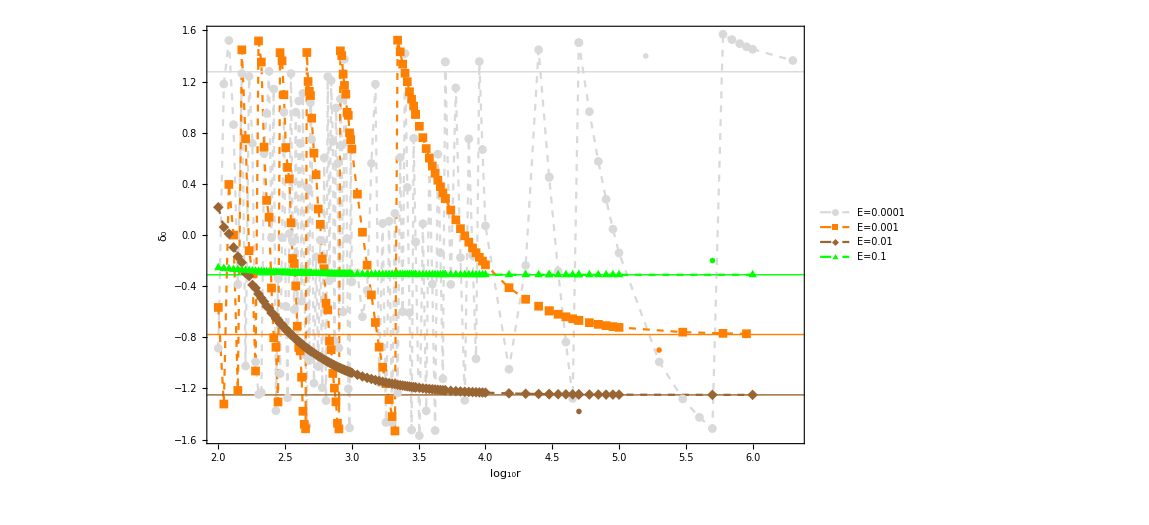

```mathematica
ListPlot[{δe1,δe2,δe3,δe4},Frame->True,FrameTicks->{{All,None},{All,None}},Joined->True,PlotMarkers->Automatic,ImageSize->850,FrameLabel->{"log_10r","δ_0"},RotateLabel->False,PlotStyle->{{Dashed,LightGray},{Dashed,Orange},{Dashed,Brown},{Dashed,Green}},Axes->None,Epilog->{{LightGray,Thin,InfiniteLine[{0,1.2760617237454488},{1,0}],Inset[Style["δ_0(E=0.0001)=1.27606",14],{5.2,1.4}]},{Orange,Thin,InfiniteLine[{0,-0.7785323639595991},{1,0}],Inset[Style["δ_0(E=0.001)=-0.778532",14],{5.3,-0.9}]},{Brown,Thin,InfiniteLine[{0,-1.2504420054816177},{1,0}],Inset[Style["δ_0(E=0.01)=-1.25044",14],{4.7,-1.38}]},{Green,Thin,InfiniteLine[{0,-0.31120281839896935},{1,0}],Inset[Style["δ_0(E=0.1)=-0.311203",14],{5.7,-0.2}]}},PlotLegends->{"E=0.0001","E=0.001","E=0.01","E=0.1"}]
Export["C:\\Users\\ASUS\\OneDrive\\Documents\\Test_6\\Test_PhaseShift_NA_Coulomb_etest1.eps",%];
```